```mathematica
f[x_]=x*Log[3,x]-5*x+x^2+2;
```

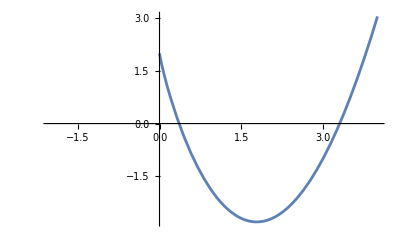

```mathematica
Plot[f[x],{x,-2,4}]
```

```mathematica
Solve[f[x]== 0]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

Solve[2-5 x+x^2+(x Log[x])/Log[3]==0]

```mathematica
NSolve[f[x]==0]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[2-5 x+x^2+(x Log[x])/Log[3]==0]

```mathematica
Roots[f[x]==0,x]
```

Roots::neq: f[x] is expected to be a polynomial in the variable x.

Roots[f[x]==0,x]

```mathematica
Factor[f[x]]
```

(2 Log[3]-5 x Log[3]+x^2 Log[3]+x Log[x])/Log[3]

```mathematica
FindRoot[f[x]==0,{x,3}]
```

{x→3.30658}

```mathematica
FindRoot[f[x]==0,{x,1}]
```

{x→0.358796}